```mathematica
(* Set directory is required for each cold start. *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
niceticks[min_,max_]:={#,NumberForm[#,DigitBlock->3],{0.02,0}}&/@FindDivisions[{min,max},6]
```

```mathematica
plot[values_]:=ListLinePlot[values, PlotLegends->{"Astro", "TURF"}, Frame->True,FrameTicks->{{niceticks,None},{Automatic,None}}]
```

Area

```mathematica
areaFiles = FileNames["./bench/run/area-*.json"];
areaJSON = Import[#1]&/@areaFiles;
areaJSONValues = Transpose@Values@areaJSON;
```

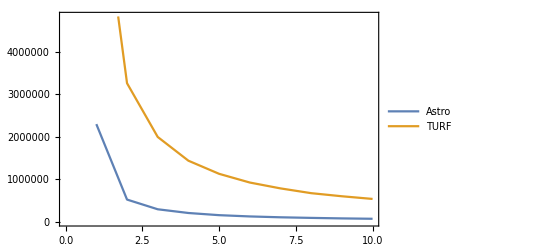

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
areaPlot = plot[areaJSONValues]
```

```mathematica
astroMean = AccountingForm@Mean[areaJSONValues[[1]]]
turfMean = AccountingForm@Mean[areaJSONValues[[2]]]
```

397021.

2003383.

```mathematica
Export["area.png",areaPlot]
```

area.png

Union

```mathematica
unionFiles = FileNames["./bench/run/union-*.json"];
unionJSON = Import[#1]&/@unionFiles;
unionJSONValues = Transpose@Values@unionJSON;
```

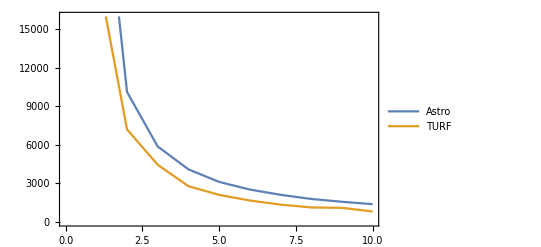

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
unionPlot = plot[unionJSONValues]
```

```mathematica
unionAstroMean = AccountingForm@Mean[unionJSONValues[[1]]]
unionTurfMean = AccountingForm@Mean[unionJSONValues[[2]]]
```

6484.14

4243.88

```mathematica
Export["union.png" , unionPlot]
```

union.png

# Difference

```mathematica
differenceFiles = FileNames["./bench/run/difference-*.json"];
differenceJSON = Import[#1]&/@differenceFiles;
differenceJSONValues = Transpose@Values@differenceJSON;
```

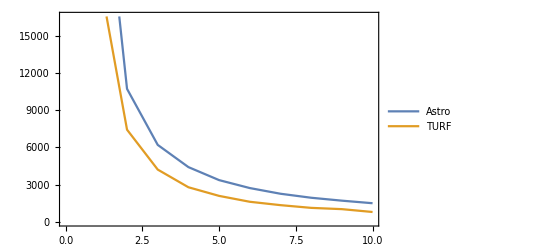

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
differencePlot =plot[differenceJSONValues]
```

```mathematica
differenceAstroMean = Mean[differenceJSONValues[[1]]]
differenceTurfMean = Mean[differenceJSONValues[[2]]]
```

6852.64

4348.88

```mathematica
Export["difference.png", differencePlot]
```

difference.png

# Intersect

```mathematica
intersectFiles = FileNames["./bench/run/intersect-*.json"];
intersectJSON = Import[#1]&/@intersectFiles;
intersectJSONValues = Transpose@Values@intersectJSON;
```

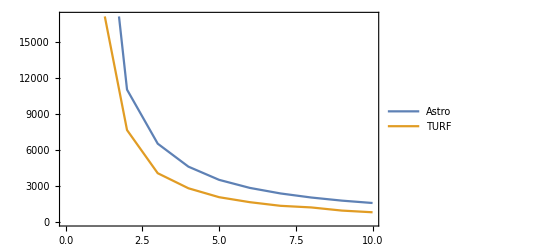

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
intersectPlot = plot[intersectJSONValues]
```

```mathematica
intersectAstroMean = Mean[intersectJSONValues[[1]]]
intersectTurfMean = Mean[intersectJSONValues[[2]]]
```

7053.39

4323.43

```mathematica
Export["intersect.png", intersectPlot]
```

intersect.png